# Аналитическое

## 2-ух частичное

```mathematica
sg1 = {{0,1},{1,0}};
sg2 = {{0,-I},{I,0}};
sg3={{1,0},{0,-1}};
i=IdentityMatrix[2];
sgp={{0,1},{0,0}};
sgm={{0,0},{1,0}};
r=1/2(i+v1[t]*sg1+v2[t]*sg2+v3[t]*sg3);
nm=sgp.sgm;
h=-Δ*nm+λχ/2(nm.nm-nm);
λ=10^-2;
Δ=1;
χ=1;
γ=1;
n0=6;
ream0=1;
imam0=0;
v10=2ream0;
v20=2imam0;
```

```mathematica
Lr=-I(h.r-r.h)+γ/2(sgm.r.sgp-1/2(nm.r+r.nm));(*Генератор и его действие в виде матрицы*)
```

```mathematica
rho[t_]:=1/2(i+(ⅇ^(-(t γ)/4) (v10 Cos[t Δ]+v20 Sin[t Δ]))sg1+(ⅇ^(-(t γ)/4) (v20 Cos[t Δ]-v10 Sin[t Δ]))sg2+(-ⅇ^(-(t γ)/2) (ⅇ^((t γ)/2)-2 n0))*sg3)(*Решение уравнения*)
```

## Сравнение с нашим 2-ух частичным(действие генератора 0)

```mathematica
ma=({{ream0-ⅈ imam0}, {ream0+ⅈ imam0}});(*Матрица средних*)
ca=({{0, 1/2+n0-ma[[1,1]]ma[[2,1]]}, {1/2+n0-ma[[1,1]]ma[[2,1]], 0}});(*матрица ковариаций*)
```

```mathematica
h={{0,-Δ},{-Δ,0}}; (*матрица гамильтониана*)
g={{0,γ/2},{0,0}};(*матрица диссипаций*)
j=({{0, -1}, {1, 0}});
mt[t_]:=MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t].ma;(*Шредингер средние*)
ct[t_]:=MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t].ca.MatrixExp[(-ⅈ h+(Transpose[g]-g)/2).j t]+∫_0^t MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)s].j.((g+Transpose[g])/2).j.MatrixExp[(-ⅈ h+(Transpose[g]-g)/2).j s]ⅆs
```

## Сравнение

```mathematica
FullSimplify[Tr[sgp.sgm.rho[t]]]
FullSimplify[ct[t][[1,2]]-1/2+mt[t][[1,1]]mt[t][[2,1]]]
```

6 ⅇ^(-t/2)

6 ⅇ^(-t/2)

```mathematica
FullSimplify[Tr[sgm.rho[t]]]
FullSimplify[mt[t][[1,1]]]
```

ⅇ^((-1/4+ⅈ) t)

ⅇ^((-1/4+ⅈ) t)

# Через Вика

## Моменты по теореме вика

```mathematica
jw = {{0,-1},{1,0}};
mw[t_]:=({{am[t]}, {ap[t]}});
apf[t_]:=mw[t][[2,1]];
amf[t_]:=mw[t][[1,1]];
cw = ({{am2[t]-am[t]am[t], 1/2+n[t]-am[t]ap[t]}, {1/2+n[t]-am[t]ap[t], ap2[t]-ap[t]ap[t]}});
cf=cw(*-j/4.(Inverse[2*j.cw]+2*j.cw)*);
am2f[t_]:=cf[[1,1]]+amf[t]^2;
ap2f[t_]:=cf[[2,2]]+apf[t]^2;
nf[t_]:=cf[[1,2]]-1/2+amf[t]*apf[t];
dpm=nf[t]-apf[t]*amf[t];
dpp=ap2f[t]-apf[t]^2;
dmm=am2f[t]-amf[t]^2;
```

```mathematica
w1m0=apf[t]
```

ap[t]

```mathematica
w0m1=amf[t]
```

am[t]

```mathematica
w0m2=am2f[t](*a^2*)//FullSimplify
```

am2[t]

```mathematica
w2m0=ap2f[t](*a^(+2)*)//FullSimplify
```

ap2[t]

```mathematica
w1m1=nf[t](*n*)//FullSimplify
```

n[t]

```mathematica
w0m6=FullSimplify[90 dmm^3+90 dmm^2*amf[t]^2+15dmm*amf[t]^4+amf[t]^6](*a^6*)
```

-14 am[t]^6+105 am[t]^4 am2[t]-180 am[t]^2 am2[t]^2+90 am2[t]^3

```mathematica
w6m0=FullSimplify[90 dpp^3+90 dpp^2*apf[t]^2+15dpp*apf[t]^4+apf[t]^6](*a^(+6)*)
```

-14 ap[t]^6+105 ap[t]^4 ap2[t]-180 ap[t]^2 ap2[t]^2+90 ap2[t]^3

```mathematica
w1m5=FullSimplify[Expand[30dpm dmm dmm +30dpm dmm amf[t]^2+30dmm dmm apf[t]*amf[t]+5dpm amf[t]^4+10dmm apf[t] amf[t]^3+apf[t]*amf[t]^5]](*a^+a^5*)
```

4 am[t]^3 (4 am[t]^2-5 am2[t]) ap[t]+5 (am[t]^4-6 am[t]^2 am2[t]+6 am2[t]^2) n[t]

```mathematica
w5m1=FullSimplify[30dpm dpp dpp +30dpm dpp apf[t]^2+30dpp dpp amf[t]*apf[t]+5dpm apf[t]^4+10dpp amf[t] apf[t]^3+amf[t]*apf[t]^5](*a^(+5)a*)
```

4 am[t] (4 ap[t]^5-5 ap[t]^3 ap2[t])+5 (ap[t]^4-6 ap[t]^2 ap2[t]+6 ap2[t]^2) n[t]

```mathematica
w0m5=FullSimplify[30dmm*dmm*amf[t]+10dmm*amf[t]^3+amf[t]^5](*a^5*)
```

21 am[t]^5-50 am[t]^3 am2[t]+30 am[t] am2[t]^2

```mathematica
w5m0=FullSimplify[30dpp*dpp*apf[t]+10dpp*apf[t]^3+apf[t]^5](*a^(+5)*)
```

21 ap[t]^5-50 ap[t]^3 ap2[t]+30 ap[t] ap2[t]^2

```mathematica
w0m4=FullSimplify[6dmm*dmm+6dmm*amf[t]^2+amf[t]^4](*a^4*)
```

am[t]^4-6 am[t]^2 am2[t]+6 am2[t]^2

```mathematica
w4m0=FullSimplify[6dpp*dpp+6dpp*apf[t]^2+apf[t]^4](*a^(+4)*)
```

ap[t]^4-6 ap[t]^2 ap2[t]+6 ap2[t]^2

```mathematica
w1m2=FullSimplify[2dpm*amf[t]+apf[t]*dmm + apf[t] amf[t]^2](*fa^+a^2 f*)
```

-2 am[t]^2 ap[t]+am2[t] ap[t]+2 am[t] n[t]

```mathematica
w2m1=FullSimplify[2dpm*apf[t]+amf[t]*dpp+apf[t]^2 amf[t]](*fa^(+^2)af*)
```

am[t] (-2 ap[t]^2+ap2[t])+2 ap[t] n[t]

```mathematica
w2m3=FullSimplify[3dpp*dmm*amf[t]+6apf[t]*dpm*dmm+6amf[t]*dpm^2+dpp*amf[t]^3+6dpm*apf[t]*amf[t]^2+3dmm*apf[t]^2 amf[t]+apf[t]^2 amf[t]^3](*a^(+^2)a^3*)
```

am[t]^3 (6 ap[t]^2-2 ap2[t])-12 am[t]^2 ap[t] n[t]+6 am2[t] ap[t] n[t]+am[t] (3 am2[t] (-2 ap[t]^2+ap2[t])+6 n[t]^2)

```mathematica
w3m2=FullSimplify[3dmm*dpp*apf[t]+6amf[t]*dpm*dpp+6apf[t]*dpm^2+dmm*apf[t]^3+6dpm*amf[t]*apf[t]^2+3dpp*amf[t]^2 apf[t]+amf[t]^2 apf[t]^3](*a^(+^3)a^2*)
```

6 am[t]^2 (ap[t]^3-ap[t] ap2[t])+6 am[t] (-2 ap[t]^2+ap2[t]) n[t]+ap[t] (am2[t] (-2 ap[t]^2+3 ap2[t])+6 n[t]^2)

```mathematica
w2m2=FullSimplify[dpp*dmm+2 dpm^2+dpp*amf[t]^2+dmm*apf[t]^2+4dpm*apf[t]*amf[t]+apf[t]^2 amf[t]^2](*a^(+^2)a^2*)
```

-2 am[t]^2 ap[t]^2+am2[t] ap2[t]+2 n[t]^2

```mathematica
w3m3=FullSimplify[36 dpm^3+9dpp dmm dpm + 36 dpm^2 apf[t]amf[t]+9dmm dpp apf[t]amf[t]+9dpm apf[t]^2 amf[t]^2+3dpp apf[t] amf[t]^3+3dmm apf[t]^3 amf[t]+apf[t]^3 amf[t]^3](*a^(+3)a^3*)
```

am[t]^3 (-14 ap[t]^3+3 ap[t] ap2[t])+9 am[t]^2 (6 ap[t]^2-ap2[t]) n[t]+9 am2[t] (-ap[t]^2+ap2[t]) n[t]+36 n[t]^3+3 am[t] (am2[t] ap[t]^3-24 ap[t] n[t]^2)

```mathematica
w0m3=FullSimplify[amf[t]^3+3dmm*amf[t]](*a^3*)
```

-2 am[t]^3+3 am[t] am2[t]

```mathematica
w3m0=FullSimplify[apf[t]^3+3dpp*apf[t]](*(a^+)^3*)
```

-2 ap[t]^3+3 ap[t] ap2[t]

```mathematica
w1m3=FullSimplify[3dpm*dmm+3dpm*amf[t]^2+3apf[t]amf[t]*dmm+apf[t] amf[t]^3](*fa^+a^3 f*)
```

-2 am[t]^3 ap[t]+3 am2[t] n[t]

```mathematica
w3m1=FullSimplify[3dpm*dpp+3dpm*apf[t]^2+3amf[t]apf[t]*dpp+apf[t]^3 amf[t]](*fa^(+3)af*)
```

-2 am[t] ap[t]^3+3 ap2[t] n[t]

```mathematica
w2m4=FullSimplify[3dpp*dmm*dmm+12 dpm^2 dmm+3dpp*dmm*amf[t]^2+12 dpm^2 amf[t]^2+24dpm*dmm*apf[t]*amf[t]+6 dmm^2 apf[t]^2+dpp*amf[t]^4+8dpm*apf[t] amf[t]^3+6dmm*apf[t]^2 amf[t]^2+apf[t]^2 amf[t]^4](*a^(+^2)a^4*)
```

-3 am[t]^2 am2[t] (5 ap[t]^2+ap2[t])+am[t]^4 (16 ap[t]^2+ap2[t])-16 am[t]^3 ap[t] n[t]+3 am2[t] (am2[t] (ap[t]^2+ap2[t])+4 n[t]^2)

```mathematica
w4m2=FullSimplify[3dmm*dpp*dpp+12 dpm^2 dpp+3dmm*dpp*apf[t]^2+12 dpm^2 apf[t]^2+24dpm*dpp*amf[t]*apf[t]+6 dpp^2 amf[t]^2+dmm*apf[t]^4+8dpm*amf[t] apf[t]^3+6dpp*amf[t]^2 apf[t]^2+amf[t]^2 apf[t]^4](*a^(+^4)a^2*)
```

am[t]^2 (16 ap[t]^4-15 ap[t]^2 ap2[t]+3 ap2[t]^2)+am2[t] (ap[t]^4-3 ap[t]^2 ap2[t]+3 ap2[t]^2)-16 am[t] ap[t]^3 n[t]+12 ap2[t] n[t]^2

```mathematica
w1m4=FullSimplify[12dpm*dmm*amf[t]+6 dmm^2 apf[t]+4dpm*amf[t]^3+6dmm*apf[t]*amf[t]^2+apf[t]*amf[t]^4](*a^+a^4*)
```

3 (3 am[t]^4-6 am[t]^2 am2[t]+2 am2[t]^2) ap[t]+4 am[t] (-2 am[t]^2+3 am2[t]) n[t]

```mathematica
w4m1=FullSimplify[12dpm*dpp*apf[t]+6 dpp^2 amf[t]+4dpm*apf[t]^3+6dpp*amf[t]*apf[t]^2+amf[t]*apf[t]^4](*a^(+4)a*)
```

3 am[t] (3 ap[t]^4-6 ap[t]^2 ap2[t]+2 ap2[t]^2)+4 ap[t] (-2 ap[t]^2+3 ap2[t]) n[t]

## Уравнение

```mathematica
f1=am[t](-γ/4+ⅈ Δ)-ⅈ λ χ w1m2;
f2=ap[t](-γ/4-ⅈ Δ)+ⅈ λ χ w2m1;
f3=-γ/2 n[t];
f4=am2[t](-γ/2+ⅈ(2Δ-λ χ))-2ⅈ λ χ w1m3;
f5=ap2[t](-γ/2-ⅈ(2Δ-λ χ))+2ⅈ λ χ w3m1;
```

```mathematica
am0=ream0-ⅈ imam0;
ap0=Conjugate[am0];
am20=0;
ap20=Conjugate[am20];
```

```mathematica
ans1=NDSolve[{am'[t]==f1,ap'[t]==f2,n'[t]==f3,am2'[t]==f4,ap2'[t]==f5,am[0]==am0,ap[0]==ap0,n[0]==n0,am2[0]==am20,ap2[0]==ap20},{am,ap,n,am2,ap2},{t,0,10}];
```

{{am→InterpolatingFunction[…],ap→InterpolatingFunction[…],n→InterpolatingFunction[…],am2→InterpolatingFunction[…],ap2→InterpolatingFunction[…]}}

## Графики

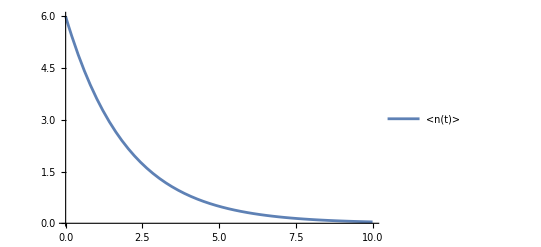

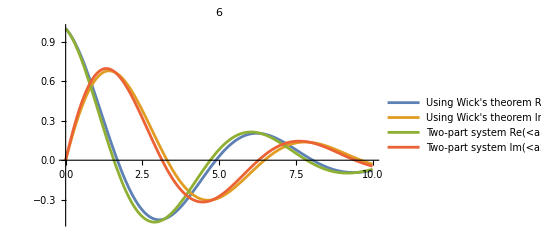

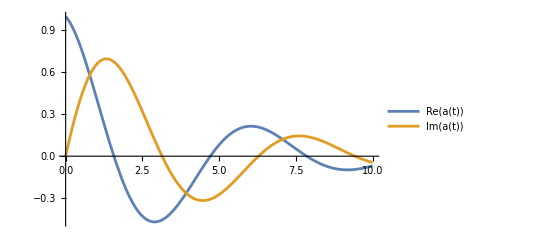

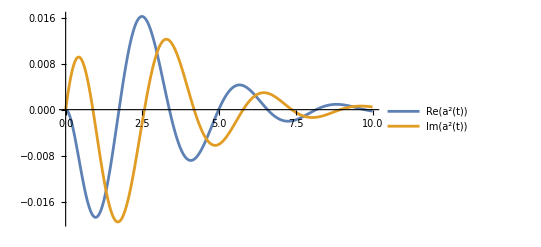

```mathematica
Plot[Re[Evaluate[n[t]/.ans1]],{t,0,10},PlotLegends->Placed[{"<n(t)>"},{Right,Top}],PlotRange->All]
Plot[{Re[Evaluate[am[t]/.ans1]],Im[Evaluate[am[t]/.ans1]],Re[Tr[sgm.rho[t]]],Im[Tr[sgm.rho[t]]]},{t,0,10},PlotLegends->Placed[{"Using Wick's theorem Re(<a>)", "Using Wick's theorem Im(<a>)", "Two-part system Re(<a>)","Two-part system Im(<a>)"},{Right, Top}],PlotLabel-> n0]
Plot[{Re[Tr[sgm.rho[t]]],Im[Tr[sgm.rho[t]]]},{t,0,10},PlotLegends->Placed[{"Re(a(t))","Im(a(t))"}, {Right,Top}]]
Plot[{Re[Evaluate[am2[t]/.ans1]],Im[Evaluate[am2[t]/.ans1]]},{t,0,10},PlotLegends->Placed[{"Re(a^2(t))","Im(a^2(t))"}, {Right,Top}]]
```

```mathematica
ans =Get["E:\\Work\\Wolfram\\Новая папка\\ans.m"];
(*ca=({{Evaluate[am2[t]/.ans]-(Evaluate[am[t]/.ans])^2, 1/2+Evaluate[n[t]/.ans]-Evaluate[am[t]/.ans]Evaluate[ap[t]/.ans]}, {1/2+Evaluate[n[t]/.ans]-Evaluate[am[t]/.ans]Evaluate[ap[t]/.ans], Evaluate[ap2[t]/.ans]-(Evaluate[ap[t]/.ans])^2}});(*матрица ковариаций*)*)
mm[t_]:=({{(Evaluate[am[t]/.ans])[[1]]}, {(Evaluate[ap[t]/.ans])[[1]]}});(*Вектор средних*)
ca=({{(Evaluate[am2[t]/.ans]-(mm[t][[1,1]])^2)[[1]], (1/2+Evaluate[n[t]/.ans]-mm[t][[1,1]]mm[t][[2,1]])[[1]]}, {(1/2+Evaluate[n[t]/.ans]-mm[t][[1,1]]mm[t][[2,1]])[[1]], (Evaluate[ap2[t]/.ans]-(mm[t][[2,1]])^2)[[1]]}});(*Матрица ковариаций*)
h={{0,-Δ},{-Δ,0}}; (*матрица гамильтониана*)
g={{0,γ/2},{0,0}};(*матрица диссипаций*)
j=({{0, -1}, {1, 0}});
i=IdentityMatrix[2];
f={{ⅈ 0},{-ⅈ 0}};
mt[t_]:=MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t].mm[t]+ⅈ(MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t]-i).Inverse[j.(ⅈ h+(Transpose[g]-g)/2)].j.f;(*Вектор средних в Шредингере*)
ct[t_]:=MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)t].ca.MatrixExp[(-ⅈ h+(Transpose[g]-g)/2).j t]+∫_0^t MatrixExp[j.(ⅈ h+(Transpose[g]-g)/2)s].j.((g+Transpose[g])/2).j.MatrixExp[(-ⅈ h+(Transpose[g]-g)/2).j s]ⅆs(*Матрица ковариаций в Шредингере*)
ams[t_]:=mt[t][[1,1]];
aps[t_]:=mt[t][[2,1]];
ns[t_]:=ct[t][[1,2]]-1/2+ams[t]aps[t];
am2s[t_]:=ct[t][[1,1]]+ams[t]^2;
ap2s[t_]:=ct[t][[2,2]]+aps[t]^2;
```

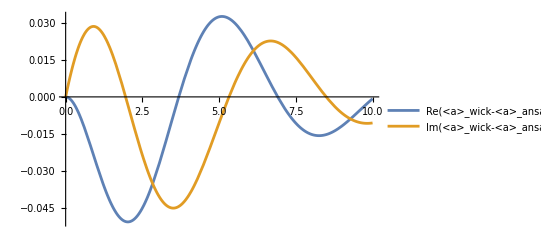

```mathematica
Plot[{Re[Evaluate[am[t]/.ans1]]-Re[ams[t]],Im[Evaluate[am[t]/.ans1]]-Im[ams[t]]},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Re(<a>_wick-<a>_ansatz)","Im(<a>_wick-<a>_ansatz)"}, {Right,Bottom}]]
```

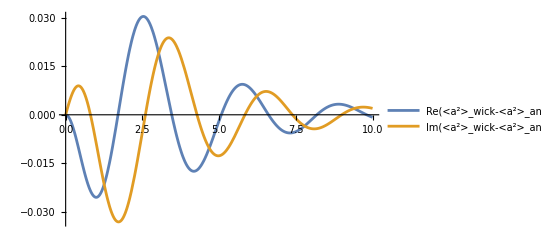

```mathematica
Plot[{Re[Evaluate[am2[t]/.ans1]]-Re[am2s[t]],Im[Evaluate[am2[t]/.ans1]]-Im[am2s[t]]},{t,0,10},PlotRange->All,PlotLegends->Placed[{"Re(<a^2>_wick-<a^2>_ansatz)","Im(<a^2>_wick-<a^2>_ansatz)"}, {Right,Bottom}]]
```

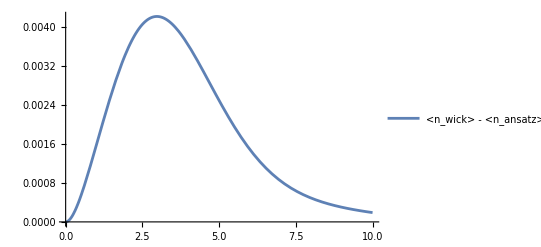

```mathematica
Plot[Re[Evaluate[n[t]/.ans1]]-Re[ns[t]],{t,0,10},PlotLegends->Placed[{"<n_wick> - <n_ansatz>"},{Right,Top}]]
```